# Example 4 - Directional derivatives and series expansion of band-structures with BandUtilities

Anirudh Chandrasekaran

23 April 2024

## Loading the Library

We first load the library by executing the following:

```mathematica
AppendTo[$Path,StringDelete[NotebookDirectory[],"/Examples"]];
<<BandUtilities`
```

When using the library for other notebooks, copy the folder “Package” on to the folder containing the notebook and add and execute the following lines instead to load the library:

AppendTo[$Path,NotebookDirectory[]<>”Package”];
<<BandUtilities`

## A simple two band model

We will define a simple two band model on the square lattice that has a non-trivial, series expandable degeneracy at the corner point (X). The X point has four fold rotational symmetry. We will obtain two bands that consist of saddles that are 90° rotated with respect to each other at X so that they satisfy the four fold symmetry together but not individually.

```mathematica
(*The lattice vectors*)
a1={1,0};
a2={0,1};

(*The Hamiltonian*)
HamltnSqr[k_,t_]:={{2t Cos[k.a1]+2t Cos[k.a2],1+ⅇ^(-ⅈ k.a2)+ⅇ^(ⅈ k.a1)+ⅇ^(ⅈ k.(a1-a2))},{1+ⅇ^(ⅈ k.a2)+ⅇ^(-ⅈ k.a1)+ⅇ^(-ⅈ k.(a1-a2)),2t Cos[k.a1]+2t Cos[k.a2]}}
```

We can plot the band structure for a sample value of the next nearest hopping t

```mathematica
HamltnTemp[k_]:=HamltnSqr[k,1/4]
```

We define the path along the Brillouin zone:

```mathematica
PltPath1={{{0,0},"Γ"},{{0,π},"M"},{{π,π},"X"},{{0,0},"Γ"}};
```

and generate the band structure along this path:

```mathematica
PltData=GenerateBandStructure[HamltnTemp,PltPath1];
```

We use plotting routine in BandUtilities to plot this

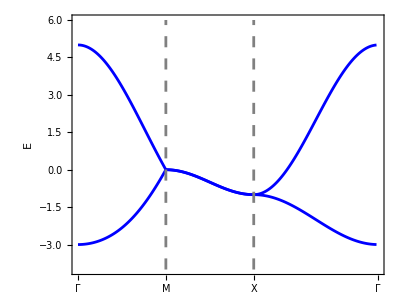

```mathematica
PlotBandStructure[PltData,{-4,6}]
```

We can see that the X point is indeed a point of non-trivial degeneracy that appears to be smooth (unlike say a nodal point). Since this is a two band model, we can find the dispersion analytically

```mathematica
{E1[{kx_,ky_},t_],E2[{kx_,ky_},t_]}=Eigenvalues[ComplexExpand[HamltnSqr[{kx,ky},t]]]
```

{1/2 (4 t Cos[kx]-8 Cos[kx/2] Cos[ky/2]+4 t Cos[ky]),1/2 (4 t Cos[kx]+8 Cos[kx/2] Cos[ky/2]+4 t Cos[ky])}

### Directional derivatives

Let us first compute the directional derivatives at a pathological point and compare it with the analytical expression. We choose a point exactly midway between the M and X points:

```mathematica
kp=1/2(PltPath1[[3,1]]+PltPath1[[2,1]])
```

{π/2,π}

We will compute the directional derivative along this direction and the one orthogonal to it

```mathematica
kd1=(PltPath1[[3,1]]-PltPath1[[2,1]])/Norm[PltPath1[[3,1]]-PltPath1[[2,1]]];
kd2=Cross[{0,0,1},Append[kd1,0]][[1;;2]];
```

We can check that these are orthogonal

```mathematica
kd2
```

{0,1}

```mathematica
kd1.kd2
```

0

Although we have chosen the direction vectors as unit vectors, we don’t have to do that. The analytical directional derivatives for both the bands are given by

```mathematica
D[E1[kp+λ kd1,1/4],λ]/.{λ->0}//N
D[E2[kp+λ kd1,1/4],λ]/.{λ->0}//N
```

-0.5

-0.5

The derivatives computed by our routine:

```mathematica
DirectionalDerivative[HamltnTemp,kp//N,kd1//N]
```

Invalid band number! Computing the directional derivative for all the bands.

{{-0.5,-0.5}}

Now for the other direction

```mathematica
D[E1[kp+λ kd2,1/4],λ]/.{λ->0}//N
D[E2[kp+λ kd2,1/4],λ]/.{λ->0}//N
```

1.41421

-1.41421

```mathematica
DirectionalDerivative[HamltnTemp,kp//N,kd2//N]
```

Invalid band number! Computing the directional derivative for all the bands.

{{-1.41421,1.41421}}

Notice that it has sorted the derivatives within a degenerate group.

### Series Expansion

We now analytically series expand the two bands at the X point. We will compare this later with the numerical series expansion

```mathematica
E1X[kx_,ky_,t_]=Normal[Series[E1[{π+λ kx,π+λ ky},t],{λ,0,4}]]/.{λ->1}
E2X[kx_,ky_,t_]=Normal[Series[E2[{π+λ kx,π+λ ky},t],{λ,0,4}]]/.{λ->1}
```

-kx ky-4 t+kx^2 t+ky^2 t+1/24 (kx^3 ky+kx ky^3-2 kx^4 t-2 ky^4 t)

kx ky-4 t+kx^2 t+ky^2 t+1/24 (-kx^3 ky-kx ky^3-2 kx^4 t-2 ky^4 t)

We can easily see that E2X is obtained from E1X by rotating (k_x,k_y) by 90° to (k_y,-k_x):

```mathematica
(E1X[kx,ky,t]-E2X[ky,-kx,t])//FullSimplify
```

0

We also plot the low energy dispersions to get a visual confirmation of this

```mathematica
Plot3D[{E1X[kx,ky,1/4],E2X[kx,ky,1/4]},{kx,-2,2},{ky,-2,2}]
```

-Graphics3D-

We are in a position to use our routine to series expand this particular case (t=1/4)

```mathematica
TaylorExpandBand[HamltnTemp,{π,π}//N,2,4]/.{p1->Subscript[k, x],p2->Subscript[k, y]}
```

k-space dimension = 2.

Parameter space (t-space) dimension = 0.

We shall attempt to series expand the given Hamiltonian at {p1,p2} = {3.14159,3.14159} to degree 4 and 0 in k and t respectively.

Invalid sample (k,t)-vector provided for numerical diagonailsation of symbolic matrix. Using the randomly generated {0.495822,0.18034} instead.

Precision of eigensystem solution at {3.14159,3.14159}, evaluated as Norm[EigVecs^*.H.EigVecs^T-DiagonalMatrix[EigVals]] = 0..

The band eigenvalues: {-1.,-1.}.

Degenerate band(s) to be series expanded: {1,2}.

Rest of the band(s): {}.

D^(0) = {{1,2}}

The symbolic, projected "derivative" matrix ℰ_1^(1) was successfully diagonalised.

Precision of the "rotated" eigensystem solution = 2.22045×10^-16.

D^(1) = {{1,2}}

The symbolic, projected "derivative" matrix ℰ_1^(2) was successfully diagonalised.

Precision of the "rotated" eigensystem solution = 2.22045×10^-16.

D^(2) = {{1},{2}}

The symbolic, projected "derivative" matrix ℰ_1^(3) was successfully diagonalised.

Precision of the "rotated" eigensystem solution = 2.22045×10^-16.

The symbolic, projected "derivative" matrix ℰ_2^(3) was successfully diagonalised.

Precision of the "rotated" eigensystem solution = 2.22045×10^-16.

D^(3) = {{1},{2}}

Computing the corrections to ℰ_1^(4)...

Done!

Computing the corrections to ℰ_2^(4)...

Done!

The symbolic, projected "derivative" matrix ℰ_1^(4) was successfully diagonalised.

Precision of the "rotated" eigensystem solution = 2.22045×10^-16.

The symbolic, projected "derivative" matrix ℰ_2^(4) was successfully diagonalised.

Precision of the "rotated" eigensystem solution = 2.22045×10^-16.

{{-1.,0,0.25 k_x^2+1. k_x k_y+0.25 k_y^2,0,-0.0208333 k_x^4-0.0416667 k_x^3 k_y-0.0416667 k_x k_y^3-0.0208333 k_y^4},{-1.,0,0.25 k_x^2-1. k_x k_y+0.25 k_y^2,0,-0.0208333 k_x^4+0.0416667 k_x^3 k_y+0.0416667 k_x k_y^3-0.0208333 k_y^4}}

We can compare this to the analytical series expansion

```mathematica
E2X[Subscript[k, x],Subscript[k, y],1/4]//N//Expand
E1X[Subscript[k, x],Subscript[k, y],1/4]//N//Expand
```

-1.+0.25 k_x^2-0.0208333 k_x^4+k_x k_y-0.0416667 k_x^3 k_y+0.25 k_y^2-0.0416667 k_x k_y^3-0.0208333 k_y^4

-1.+0.25 k_x^2-0.0208333 k_x^4-1. k_x k_y+0.0416667 k_x^3 k_y+0.25 k_y^2+0.0416667 k_x k_y^3-0.0208333 k_y^4

We see that they exactly agree. We can also series expand the general t dependent dispersion around t=1/4, using our routine. Let us turn off messages

```mathematica
HamSeries[k_]:=HamltnSqr[k[[1;;2]],k[[3]]]
```

```mathematica
Series2=TaylorExpandBand[HamSeries,{π,π,1/4}//N,2,4,"Messages"->False]/.{p3->δt};
```

```mathematica
Total[Series2[[1]]]/.{p1->Subscript[k, x],p2->Subscript[k, y]}//Sort
Total[Series2[[2]]]/.{p1->Subscript[k, x],p2->Subscript[k, y]}//Sort
```

-1.-4. δt+0.25 k_x^2+1. δt k_x^2-0.0208333 k_x^4+1. k_x k_y-0.0416667 k_x^3 k_y+0.25 k_y^2+1. δt k_y^2-0.0416667 k_x k_y^3-0.0208333 k_y^4

-1.-4. δt+0.25 k_x^2+1. δt k_x^2-0.0208333 k_x^4-1. k_x k_y+0.0416667 k_x^3 k_y+0.25 k_y^2+1. δt k_y^2+0.0416667 k_x k_y^3-0.0208333 k_y^4

Comparing this with the analytical series expansion

```mathematica
E2X[Subscript[k, x],Subscript[k, y],1/4+δt]//N//Expand//Sort
E1X[Subscript[k, x],Subscript[k, y],1/4+δt]//N//Expand//Sort
```

-1.-4. δt+0.25 k_x^2+δt k_x^2-0.0208333 k_x^4-0.0833333 δt k_x^4+k_x k_y-0.0416667 k_x^3 k_y+0.25 k_y^2+δt k_y^2-0.0416667 k_x k_y^3-0.0208333 k_y^4-0.0833333 δt k_y^4

-1.-4. δt+0.25 k_x^2+δt k_x^2-0.0208333 k_x^4-0.0833333 δt k_x^4-1. k_x k_y+0.0416667 k_x^3 k_y+0.25 k_y^2+δt k_y^2+0.0416667 k_x k_y^3-0.0208333 k_y^4-0.0833333 δt k_y^4

These clearly agree except for the δt correction for the quartic terms. This requires series expansion to 5^th degree jointly in k and t which the routine cannot presently handle in the cases of complicated degeneracies.